# Лабораторная работа 2. Структура выражения.

Выполнила студентка ММФ БГУ
Вариант 8. КМ, 1 к, 5 гр. Шклярик В.С.
  15 сентября 2021

## 1. Построение дерева выражения

### Задание 1.1

Введите два математических выражения, каждое – в отдельную вычисляемую ячейку: выражение (1.1) и Ваш вариант из предложенной ниже 
таблицы.

```mathematica
(- 1)/5+ⅇ+(1-2ⅈ)/(-.4*x+3*y)-7π*x*z+z^(6x)
```

```mathematica
1/(a-b*x^2)
```

Superscript ctrl6, Fraction ctrl/,  Radical ctrl2

π EscpiEcs, ∞ EscInfEsc, ⅇ EsceeEsc

### Задание 1.2

#### 2)

```mathematica
(1-2ⅈ)/(2*y-.1*x)-1/3+z^(4*x)//StandardForm
```

-1/3+(1-2 ⅈ)/(-0.1 x+2 y)+z^(4 x)

#### 3)

```mathematica
(1-2ⅈ)/(2*y-.1*x)-1/3+z^(4*x)//FullForm
```

Plus[Rational[-1,3],Times[Complex[1,-2],Power[Plus[Times[-0.1,x],Times[2,y]],-1]],Power[z,Times[4,x]]]

#### 4)

С помощью функции FullForm можно понять, как построить дерево выражения по заданной формуле.

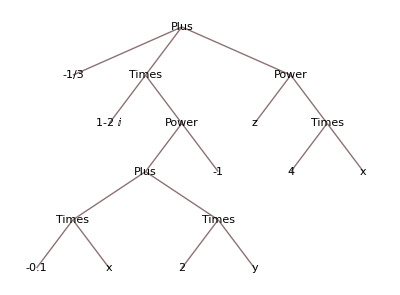

```mathematica
(1-2ⅈ)/(2*y-.1*x)-1/3+z^(4*x)//TreeForm
```

С помощью функции TreeForm можно построить дерево выражения по заданной формуле.

#### 5),6)

```mathematica
expr1=((- 1)/5+ⅇ+(1-2ⅈ)/(-.4*x+3*y)-7π*x*z+z^(6x))
```

```mathematica
myExpr=1/(a-b*x^2)
```

```mathematica
?expr1
```

```mathematica
?myExpr
```

#### 7)

```mathematica
expr1//FullForm
```

Plus[Rational[-1,5],E,Times[Complex[1,-2],Power[Plus[Times[-0.4,x],Times[3,y]],-1]],Times[-7,Pi,x,z],Power[z,Times[6,x]]]

```mathematica
myExpr//StandardForm
```

1/(a-b x^2)

#### 9)

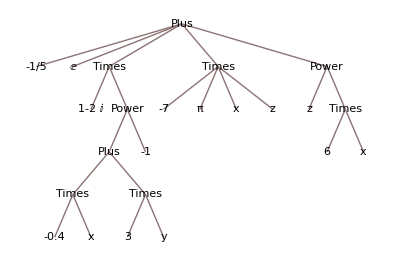

```mathematica
expr1//TreeForm
```

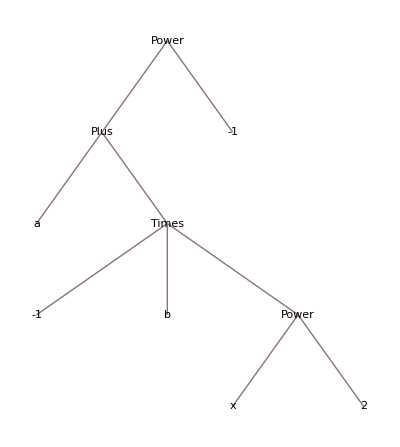

```mathematica
myExpr//TreeForm
```

#### 10)

Результат выполнения функции ExprAsTree, представленный на рис 2.1 совпадает с результатом выполнения встроенной функции TreeForm

## 2. Анализ структуры выражения

### Задание 2.1

Изучите возможности исследования структуры выражения посредством функций Level, Depth. Используйте в качестве примеров выражение (1.1) и выражение Вашего варианта.

#### 4)

```mathematica
expr1=((- 1)/5+ⅇ+(1-2ⅈ)/(-.4*x+3*y)-7π*x*z+z^(6x))
```

```mathematica
myExpr=1/(a-b*x^2)
```

```mathematica
?myExpr
```

```mathematica
?expr1
```

#### 5)

```mathematica
TreeForm[expr1]
```

-Graphics-

```mathematica
TreeForm[myExpr]
```

-Graphics-

#### 7)

```mathematica
Level[expr1,{0}]
```

{-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x)}

```mathematica
Level[expr1,{1}]
```

{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),-7 π x z,z^(6 x)}

```mathematica
Level[expr1,{2}]
```

{1-2 ⅈ,1/(-0.4 x+3 y),-7,π,x,z,z,6 x}

```mathematica
Level[expr1,{3}]
```

{-0.4 x+3 y,-1,6,x}

```mathematica
Level[expr1,{4}]
```

{-0.4 x,3 y}

```mathematica
Level[expr1,{5}]
```

{-0.4,x,3,y}

```mathematica
Level[expr1,{6}]
```

{}

#### 8)

Уровень 0 соответствует всему выражению.
Функция Level возвращает выражение в виде списка.

#### 9),10)

```mathematica
Depth[expr1]
```

6

Все подвыражения expr1 расположены на уровнях от 0 до Depth[expr1]-1.
Последний уровень имеет номер Depth[expr1]-1.

Максимальное  натуральное число n, при котором вычисленное выражение Level[expr1,{n}] возвращает непустой список равно 5, это как раз Depth[expr1]-1.

#### 11)

```mathematica
Level[expr1,{-1}]
```

{-1/5,ⅇ,1-2 ⅈ,-0.4,x,3,y,-1,-7,π,x,z,z,6,x}

```mathematica
Level[expr1,{-2}]
```

{-0.4 x,3 y,-7 π x z,6 x}

#### 12)

```mathematica
Level[expr1,{Depth[expr1]-1}]
```

{-0.4,x,3,y}

```mathematica
Level[expr1,{Depth[expr1]-2}]
```

{-0.4 x,3 y}

### Задание 2.2

Форматируйте структуру выражения (1.1), используя функции Head, Table, MatrixForm. Используйте чистые (анонимные, безымянные) функции и функцию Map.

#### 1)

Dopaclet:ref/Do[expr,n] вычисляет expr n раз, Dopaclet:ref/Do[expr,{i,i_max}] вычисляет expr с переменной i, последовательно принимая значения от 1 до i max (с шагом 1).
Tablepaclet:ref/Table[expr,n] генерирует список из n копий expr, Tablepaclet:ref/Table[expr,{i,i_max}] генерирует список значений expr, когда i изменяется от 1 до i max.

#### 2)

```mathematica
Table[Level[expr1,{i}],{i,0,Depth[expr1]-1}]
```

{{-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x)},{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),-7 π x z,z^(6 x)},{1-2 ⅈ,1/(-0.4 x+3 y),-7,π,x,z,z,6 x},{-0.4 x+3 y,-1,6,x},{-0.4 x,3 y},{-0.4,x,3,y}}

#### 3)

```mathematica
Table[Level[expr1,{i}],{i,0,Depth[expr1]-1}]//MatrixForm
```

({-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x)}
{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),-7 π x z,z^(6 x)}
{1-2 ⅈ,1/(-0.4 x+3 y),-7,π,x,z,z,6 x}
{-0.4 x+3 y,-1,6,x}
{-0.4 x,3 y}
{-0.4,x,3,y})

#### 4)

```mathematica
Head/@Level[expr1,{3}]
```

{Plus,Integer,Integer,Symbol}

#### 5)

```mathematica
Table[Head/@Level[expr1,{i}],{i,0,Depth[expr1]-1}]//MatrixForm
```

({Plus}
{Rational,Symbol,Times,Times,Power}
{Complex,Power,Integer,Symbol,Symbol,Symbol,Symbol,Times}
{Plus,Integer,Integer,Symbol}
{Times,Times}
{Real,Symbol,Integer,Symbol})

#### 6),7),8)

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{1}]
```

{(Rational
-1/5),(Symbol
ⅇ),(Times
(1-2 ⅈ)/(-0.4 x+3 y)),(Times
-7 π x z),(Power
z^(6 x))}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{2}]
```

{(Complex
1-2 ⅈ),(Power
1/(-0.4 x+3 y)),(Integer
-7),(Symbol
π),(Symbol
x),(Symbol
z),(Symbol
z),(Times
6 x)}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{3}]
```

{(Plus
-0.4 x+3 y),(Integer
-1),(Integer
6),(Symbol
x)}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{4}]
```

{(Times
-0.4 x),(Times
3 y)}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{5}]
```

{(Real
-0.4),(Symbol
x),(Integer
3),(Symbol
y)}

#### 9)

```mathematica
Table[MatrixForm[{Head[#],#}]&/@Level[expr1,{i}],{i,0,Depth[expr1]-1}]//MatrixForm
```

({(Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x))}
{(Rational
-1/5),(Symbol
ⅇ),(Times
(1-2 ⅈ)/(-0.4 x+3 y)),(Times
-7 π x z),(Power
z^(6 x))}
{(Complex
1-2 ⅈ),(Power
1/(-0.4 x+3 y)),(Integer
-7),(Symbol
π),(Symbol
x),(Symbol
z),(Symbol
z),(Times
6 x)}
{(Plus
-0.4 x+3 y),(Integer
-1),(Integer
6),(Symbol
x)}
{(Times
-0.4 x),(Times
3 y)}
{(Real
-0.4),(Symbol
x),(Integer
3),(Symbol
y)})

### Задание 2.3

Изучите возможности исследования структуры выражения посредством функций AtomQ, Position, Part, Take, Length. Используйте 
выражение (1.1) в качестве примера.

#### 1)

```mathematica
Position[expr1,x]
```

{{3,2,1,1,2},{4,3},{5,2,2}}

```mathematica
Position[expr1,y]
```

{{3,2,1,2,2}}

```mathematica
Position[expr1,z]
```

{{4,4},{5,1}}

#### 2)

```mathematica
expr1⟦-1⟧
```

z^(6 x)

```mathematica
expr1⟦-2⟧
```

-7 π x z

```mathematica
expr1⟦-1,1⟧
```

z

```mathematica
Take[expr1,{-2,-1}]
```

-7 π x z+z^(6 x)

```mathematica
Take[Level[expr1,{2}],{-2}]
```

{z}

#### 3)

```mathematica
AtomQ/@Table[Level[expr1,{1}]]
```

{True,True,False,False,False}

#### 4)

Part используется для извлечения подвыражения выражения.
Take используется для извлечения конкретного элемента из списка.
AtomQ возвращает True, если выражение является таким, что его нельзя разделить на подвыражения, и возвращает False в противном случае.

## 3. Разложение выражения по уровням

### Задание 3.1

Создайте функцию myExprLevels[expr], возвращающую произвольное выражение expr в виде подвыражений, разложенных по уровням. Для каждого уровня выражения expr функция myExprLevels отображает подвыражения, которые находятся на указанном уровне, а также головы этих подвыражений.

```mathematica
myExprLevels[expr_]:=Do[Print[i,":",MatrixForm[{Head[#],#}]&/@Level[expr,{i}]],{i,0,Depth[expr]-1}]
```

```mathematica
myExprLevels[expr1]
```

0:{(Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x))}

1:{(Rational
-1/5),(Symbol
ⅇ),(Times
(1-2 ⅈ)/(-0.4 x+3 y)),(Times
-7 π x z),(Power
z^(6 x))}

2:{(Complex
1-2 ⅈ),(Power
1/(-0.4 x+3 y)),(Integer
-7),(Symbol
π),(Symbol
x),(Symbol
z),(Symbol
z),(Times
6 x)}

3:{(Plus
-0.4 x+3 y),(Integer
-1),(Integer
6),(Symbol
x)}

4:{(Times
-0.4 x),(Times
3 y)}

5:{(Real
-0.4),(Symbol
x),(Integer
3),(Symbol
y)}

### Задание 3.2

Разложите выражение (1.1) по уровням, используя функцию myExprLevels, построенную ранее. Определите позицию каждого атомарного объекта выражения (1.1). Результаты оформите в виде таблиц.

```mathematica
Print[{Table[Level[expr1,{-1}],{1}]}, {Position[expr1,z], Position[expr1,-1/5], Position[expr1,ⅇ], Position[expr1,1-2ⅈ], Position[expr1,-0.4], Position[expr1,x], Position[expr1,y], Position[expr1,-1], Position[expr1,-7], Position[expr1,π], Position[expr1,6],Position[expr1,3]}]
```

{{{-1/5,ⅇ,1-2 ⅈ,-0.4,x,3,y,-1,-7,π,x,z,z,6,x}}}{{{4,4},{5,1}},{{1}},{{2}},{{3,1}},{{3,2,1,1,1}},{{3,2,1,1,2},{4,3},{5,2,2}},{{3,2,1,2,2}},{{3,2,2}},{{4,1}},{{4,2}},{{5,2,1}},{{3,2,1,2,1}}}

```mathematica
Grid[{{-1/5,ⅇ,1-2 ⅈ,-0.4,x,3,y,z,-1,-7,π,6},{{{4,4},{5,1}},{{1}},{{2}},{{3,1}},{{3,2,1,1,1}},{{3,2,1,1,2},{4,3},{5,2,2}},{{3,2,1,2,2}},{{3,2,2}},{{4,1}},{{4,2}},{{5,2,1}},{{3,2,1,2,1}}}},Frame->All]
```

-1/5 | ⅇ | 1-2 ⅈ | -0.4 | x | 3 | y | z | -1 | -7 | π | 6
{{4,4},{5,1}} | {{1}} | {{2}} | {{3,1}} | {{3,2,1,1,1}} | {{3,2,1,1,2},{4,3},{5,2,2}} | {{3,2,1,2,2}} | {{3,2,2}} | {{4,1}} | {{4,2}} | {{5,2,1}} | {{3,2,1,2,1}}

## 4. Анализ моего выражения, вариант 8

### Задание 4

```mathematica
?myExpr
```

```mathematica
TreeForm[myExpr]
```

-Graphics-

```mathematica
Level[myExpr,{0}]
```

{1/(a-b x^2)}

```mathematica
Level[myExpr,{1}]
```

{a-b x^2,-1}

```mathematica
Level[myExpr,{2}]
```

{a,-b x^2}

```mathematica
Level[myExpr,{3}]
```

{-1,b,x^2}

```mathematica
Level[myExpr,{4}]
```

{x,2}

```mathematica
Level[myExpr,{5}]
```

{}

```mathematica
Depth[myExpr]
```

5

```mathematica
Table[Level[myExpr,{i}],{i,0,Depth[myExpr]-1}]
```

{{1/(a-b x^2)},{a-b x^2,-1},{a,-b x^2},{-1,b,x^2},{x,2}}

```mathematica
Table[Level[myExpr,{i}],{i,0,Depth[myExpr]-1}]//MatrixForm
```

({1/(a-b x^2)}
{a-b x^2,-1}
{a,-b x^2}
{-1,b,x^2}
{x,2})

```mathematica
Table[MatrixForm[{Head[#],#}]&/@Level[myExpr,{i}],{i,0,Depth[myExpr]-1}]//MatrixForm
```

({(Power
1/(a-b x^2))}
{(Plus
a-b x^2),(Integer
-1)}
{(Symbol
a),(Times
-b x^2)}
{(Integer
-1),(Symbol
b),(Power
x^2)}
{(Symbol
x),(Integer
2)})

```mathematica
Position[myExpr,x]
```

{{1,2,3,1}}

```mathematica
Position[myExpr,b]
```

{{1,2,2}}

```mathematica
AtomQ/@Table[Level[myExpr,{4}]]
```

{True,True}

```mathematica
myExprLevels[expr_]:=Do[Print[i,":",MatrixForm[{Head[#],#}]&/@Level[expr,{i}]],{i,0,Depth[expr]-1}]
```

```mathematica
myExprLevels[myExpr]
```

0:{(Power
1/(a-b x^2))}

1:{(Plus
a-b x^2),(Integer
-1)}

2:{(Symbol
a),(Times
-b x^2)}

3:{(Integer
-1),(Symbol
b),(Power
x^2)}

4:{(Symbol
x),(Integer
2)}

```mathematica
Print[{Table[Level[myExpr,{-1}],{1}]}, {Position[myExpr,-1], Position[myExpr,a], Position[myExpr,b], Position[myExpr,x], Position[myExpr,2]}]
```

{{{a,-1,b,x,2,-1}}}{{{1,2,1},{2}},{{1,1}},{{1,2,2}},{{1,2,3,1}},{{1,2,3,2}}}

```mathematica
Grid[{{-1,a,b,x,2},{{{1,2,1},{2}},{{1,1}},{{1,2,2}},{{1,2,3,1}},{{1,2,3,2}}}},Frame->All]
```

-1 | a | b | x | 2
{{1,2,1},{2}} | {{1,1}} | {{1,2,2}} | {{1,2,3,1}} | {{1,2,3,2}}